#### Contains functions defined in “Q-balls stopping power” file

```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Charged Pion-Carbon scattering

```mathematica
Emaxfull:=(2M*β^2*γ^2)/(1+2γ*(M/mπ)+(M/mπ)^2)
```

```mathematica
Emaxfull/.{M->1000*12,β->0.95,γ->5,mπ->139.57}
```

65.612

```mathematica
dσdE/.me->M
```

(2 π Z^2 α^2 (1-(Ed β^2)/emax))/(Ed^2 M β^2)

#### Mass of carbon nuclei (from Wolfram Alpha)

```mathematica
Convert[1.993*10^-23 Gram*SpeedOfLight^2,Mega ElectronVolt]
```

11179.9 ElectronVolt Mega

```mathematica
dEdxcarbon=2Pi*(n*Z^2*α^2)/(M*β^2)(Log[Emaxfull/emin]-β^2)/.{γ->1/Sqrt[1-β^2]}/.{β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)}//FullSimplify;
```

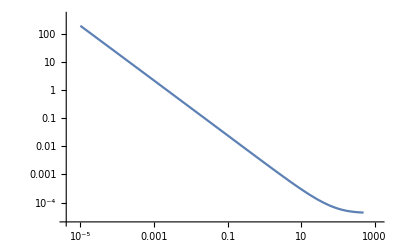

```mathematica
LogLogPlot[dEdxcarbon/.{n->0.8,me->0.511,M->11180,emin->10^-20,α->1/137,mπ->139.57,Z->6},{Eπ,0.00001,500}]
```

```mathematica
Table[Convert[(NIntegrate[dEdxcarbon^-1/.{n->0.8,me->0.511,M->11180,emin->10^-20,α->1/137,mπ->139.57,Z->6},{Eπ,0,500}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{n,{0.0008,0.008,0.08,0.8}}]
```

{0.187769 Centimeter,0.0187769 Centimeter,0.00187769 Centimeter,0.000187769 Centimeter}

```mathematica
dEdxcarbonmax=Integrate[(2 π Z^2 α^2 (1-(Ed β^2)/emax))/(Ed^2 M β^2)*n*Ed,{Ed,emin,Min[2M*γ^2*α^2,emax]}]/.{emax->Emaxfull}/.{γ->1/Sqrt[1-β^2]}/.{β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)}/.{M->11180,α->1/137,mπ->139.57,Z->6,emin->10^-20}//Simplify;
```

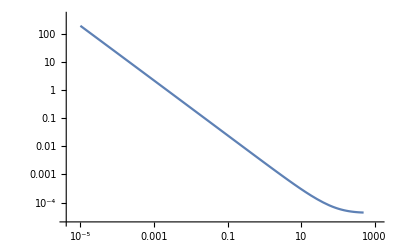

```mathematica
LogLogPlot[dEdxcarbonmax/.n->0.8,{Eπ,0.00001,500}]
```

```mathematica
Table[Convert[(NIntegrate[dEdxcarbonmax^-1,{Eπ,0,500}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{n,{0.0008,0.008,0.08,0.8}}]
```

{0.189082 Centimeter,0.0189082 Centimeter,0.00189082 Centimeter,0.000189082 Centimeter}

#### Stopping power due to radiation of charged pion (according to Rossi)

```mathematica
F=16/3(1-v)(Log[2 U/(mπ^2*rn)*(1-v)/v]-1/2)/.{v->k/U}/.{U->Eπ+mπ,rn->0.5 α/me*6^(1/3)}//FullSimplify
```

16/3 (1-k/(Eπ+mπ)) (-1/2+Log[-(2.20128 me (-1. Eπ+k-1. mπ) (Eπ+mπ))/(k mπ^2 α)])

```mathematica
stoppingrad=Integrate[n*(α^3*Z^2/(mπ^2 k)*F)*k/.{n->0.8,mπ->139.57,me->0.511,α->1/137,Z->6},k]//FullSimplify;
```

```mathematica
dEdxrad=(stoppingrad/.k->Eπ)-(stoppingrad/.k->0.0000001)//FullSimplify;
```

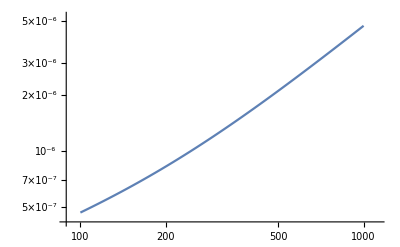

```mathematica
LogLogPlot[dEdxrad//FullSimplify,{Eπ,100,1000}]
```

#### Ignoring the logarithmic F factor (naive order of magnitude)

```mathematica
stoppingradsimple=Integrate[n*α^3*Z^2/(mπ^2 k)*k/.{n->0.8,mπ->139.57,me->0.511,α->1/137,Z->6},{k,0,Eπ}];
```

```mathematica
stoppingradsimple
```

5.74972×10^-10 Eπ

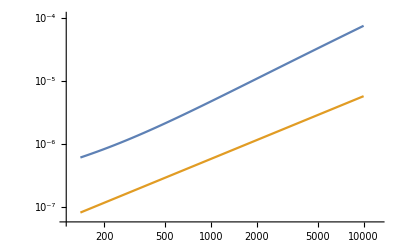

```mathematica
LogLogPlot[{dEdxrad/.n->0.8,stoppingradsimple/.n->0.8},{Eπ,140,10000}]
```

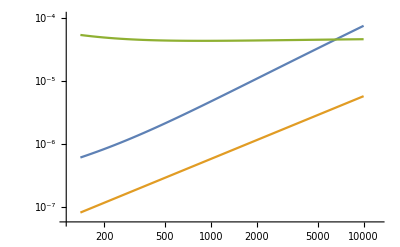

```mathematica
LogLogPlot[{dEdxrad,stoppingradsimple,dEdxcarbonmax/.n->0.8},{Eπ,140,10000}]
```

#### Evidently, the two stopping powers are equal at a critical energy of ~ 5 GeV. We can ignore radiation for all intent and purposes.

#### Check the critical energy for electron scattering, which should match PDG since density scales equally

```mathematica
stoppingpower/.{n->0.8,me->0.511,emin->10^-10,α->1/137,mπ->139.57,Z->1}
```

(0.000524092 (-Eπ (279.14+Eπ)+(139.57+Eπ)^2 Log[524646. Eπ (279.14+Eπ)]))/(Eπ (279.14+Eπ))

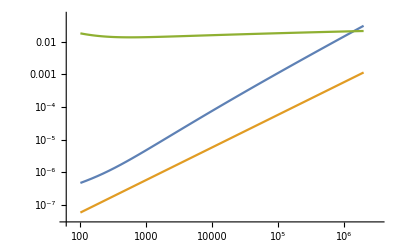

```mathematica
LogLogPlot[{dEdxrad/.n->0.8,stoppingradsimple/.n->0.8,stoppingpower/.{n->0.8,me->0.511,emin->10^-10,α->1/137,mπ->139.57,Z->1}},{Eπ,100,1000*2000}]
```

#### The critical energy for nondegenerate pion-electron collision is ~ 1000 GeV, as expected from the PDG.